Spread of the outcoming beam as a function of slab lendth for different vaules of albedo parameter

```mathematica
SetDirectory[NotebookDirectory[]]

Data1=Partition[Flatten[Import["test3.txt","Table"]],2];
```

/Users/Maria/Dropbox/Research/Alfano_group/code/beam_profile/Mie/github

```mathematica
Data2=Partition[Flatten[Import["test6.txt","Table"]],2];
```

```mathematica
Data3=Partition[Flatten[Import["test9.txt","Table"]],2];
```

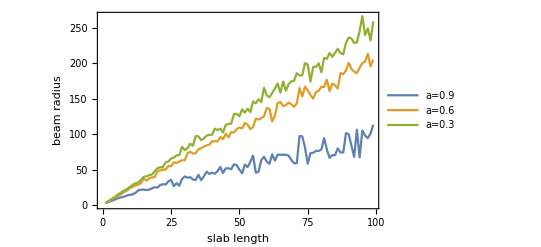

```mathematica
ListLinePlot[{Data1,Data2,Data3}, PlotLegends->{"a=0.9","a=0.6","a=0.3"},Frame->True, FrameLabel->{"slab length","beam radius"}]
```